## Part 1

test of sigma matrix reconstruction (building full measurement matrix)

```mathematica
quad[f_]:={{1,0},{1/f,1}};
drift[l_]:={{1,l},{0,1}};
testLattice[f_,l_]:=drift[l/2].quad[f].drift[l].quad[-f].drift[l/2]
```

```mathematica
testLattice[1,#] &/@ Range[10]
```

{{{-1/2,7/4},{-1,3/2}},{{-3,2},{-2,1}},{{-13/2,-3/4},{-3,-1/2}},{{-11,-8},{-4,-3}},{{-33/2,-85/4},{-5,-13/2}},{{-23,-42},{-6,-11}},{{-61/2,-287/4},{-7,-33/2}},{{-39,-112},{-8,-23}},{{-97/2,-657/4},{-9,-61/2}},{{-59,-230},{-10,-39}}}

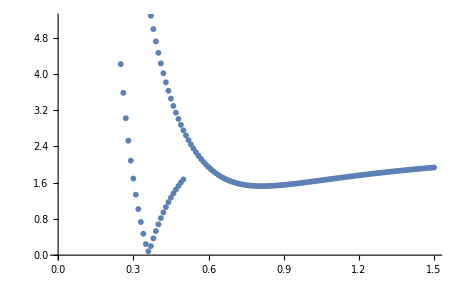

```mathematica
fVals=Join@@{Range[-0.25,-0.5,-.01] ,Range[0.25,1.5,0.01]};
rMats=Simplify[testLattice[#,1]]&/@fVals;

sigmasTracked=#.{{1,0.4},{0.4,1}}.Transpose[#]&/@rMats;
ListPlot[
Abs@Transpose[{
fVals,
Sqrt@sigmasTracked[[;;,1,1]]
}]
]
```

```mathematica
fVals=Range[0.2,1.0,0.1];
rXFODO=testLattice[#,1]&/@fVals;
rYFODO=testLattice[-#,1]&/@fVals;
```

```mathematica
make4x4[x2x2_,y2x2_]:=Join@@{
PadRight[#,4]&/@x2x2,
PadLeft[#,4]&/@y2x2
};
allRs1=Table[make4x4[rXFODO[[i]],rYFODO[[i]]],{i,1,Length@fVals}];
(*
We want to reconstruct inputSigma, using outputSigmas parts {1,1},{3,3},and{1,3} as 'measurements' 
*)
(*inputSigma={{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}};*)
ρs1=(#+Transpose[#])&@(
Join@@{
PadLeft[#,4]&/@Table[RandomReal[{-1,1},i],{i,3,1,-1}],
{{0,0,0,0}}
});
σs1=RandomReal[{1,5},4];
inputSigma1=Table[
If[
i==j,
σs1[[i]]^2,
σs1[[i]]*σs1[[j]]*ρs1[[i,j]]
],{i,1,4},{j,1,4}];
outputSigmas1=#.inputSigma1.Transpose[#]&/@allRs1;
measurements1={#[[1,1]],#[[3,3]],#[[1,3]]}&/@outputSigmas1;
measurements1=Flatten[measurements1]
```

{2743.24,288.656,1043.14,657.49,9.93271,78.8505,244.765,2.64815,-6.26666,116.627,13.5244,-4.12782,65.731,23.0862,7.09227,42.161,30.1733,16.8555,30.064,35.3945,24.1805,23.3959,39.3278,29.5272,19.5322,42.3704,33.4369}

```mathematica
ClearAll[r1,σ1,orderedSigmas1,generalMeasurementTest1]
{orderedSigmas1,generalMeasurementTest1}=Module[
{
rmat1=Table[r1[i,j],{i,1,4},{j,1,4}],
σmat1=Table[σ1[Min[i,j],Max[i,j]],{i,1,4},{j,1,4}],
unknowns1,
trans1,coefficients1,dummy1=Array[0&,{10,3}]
},
trans1=(rmat1.σmat1.Transpose[rmat1])[[Sequence@@#]]&/@{{1,1},{3,3},{1,3}};(*Take elements xx,yy,xy from σ'*)
unknowns1=DeleteDuplicates[Flatten[σmat1]];(*This is how our unknown column vector will be ordered, so we'll save it at the end.*)
coefficients1=Table[{#,Coefficient[trans1[[i]],#,1]}&/@unknowns1,{i,1,Length@trans1}];(*We extract the coeffecients in terms of r for each element of σ, each unknown.*)
{unknowns1,Table[coefficients1[[i,j,2]],{i,1,Length@trans1},{j,1,Length@unknowns1}]}
];

uncoupledMeasurementTest1=generalMeasurementTest1/.{r1[1,3]->0,r1[1,4]->0,r1[2,3]->0,r1[2,4]->0,r1[3,1]->0,r1[3,2]->0,r1[4,2]->0,r1[4,1]->0};

fullUncoupledTest1=Join@@Table[
uncoupledMeasurementTest1/.Flatten[Table[r1[i,j]->r1[scanIndex][i,j],{i,1,4},{j,1,4}]],
{scanIndex,1,Length@allRs1}
];
MatrixForm@fullUncoupledTest1;

For[
i=1,i≤Length@allRs1,i++,
rules1={r1[i][1,1]->allRs1[[i]][[1,1]],r1[i][1,2]->allRs1[[i]][[1,2]],
r1[i][2,1]->allRs1[[i]][[2,1]],r1[i][2,2]->allRs1[[i]][[2,2]],
r1[i][3,3]->allRs1[[i]][[3,3]],r1[i][3,4]->allRs1[[i]][[3,4]],
r1[i][4,3]->allRs1[[i]][[4,3]],r1[i][4,4]->allRs1[[i]][[4,4]]};
fullUncoupledTest1=fullUncoupledTest1/.rules1;
]
ClearAll[i];

MatrixForm@fullUncoupledTest1
```

(272.25 | 140.25 | 0 | 0 | 18.0625 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 42.25 | 55.25 | 18.0625
0 | 0 | 107.25 | 70.125 | 0 | 27.625 | 18.0625 | 0 | 0 | 0
62.2346 | 12.2716 | 0 | 0 | 0.604938 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.49383 | 1.90123 | 0.604938
0 | 0 | 9.64198 | 6.1358 | 0 | 0.950617 | 0.604938 | 0 | 0 | 0
21.3906 | -4.04688 | 0 | 0 | 0.191406 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.140625 | 0.328125 | 0.191406
0 | 0 | -1.73438 | -2.02344 | 0 | 0.164063 | 0.191406 | 0 | 0 | 0
9. | -6. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 2. | 1.
0 | 0 | -3. | -3. | 0 | 1. | 1. | 0 | 0 | 0
4.22531 | -5.36728 | 0 | 0 | 1.70448 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.63272 | 3.33642 | 1.70448
0 | 0 | -2.62654 | -2.68364 | 0 | 1.66821 | 1.70448 | 0 | 0 | 0
2.09954 | -4.31737 | 0 | 0 | 2.21949 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.98292 | 4.19575 | 2.21949
0 | 0 | -2.0404 | -2.15868 | 0 | 2.09788 | 2.21949 | 0 | 0 | 0
1.06348 | -3.31934 | 0 | 0 | 2.59009 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.15723 | 4.72754 | 2.59009
0 | 0 | -1.51465 | -1.65967 | 0 | 2.36377 | 2.59009 | 0 | 0 | 0
0.530559 | -2.46395 | 0 | 0 | 2.86069 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.23152 | 5.05319 | 2.86069
0 | 0 | -1.0881 | -1.23198 | 0 | 2.5266 | 2.86069 | 0 | 0 | 0
0.25 | -1.75 | 0 | 0 | 3.0625 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.25 | 5.25 | 3.0625
0 | 0 | -0.75 | -0.875 | 0 | 2.625 | 3.0625 | 0 | 0 | 0)

```mathematica
fullUncoupledTest1 //MatrixForm;
measurements1 //MatrixForm;
finalTest1=LeastSquares[fullUncoupledTest1,measurements1]
```

{10.9738,-2.28061,9.88386,-4.22733,4.17884,4.97621,7.86557,10.1394,-10.5033,24.3915}

```mathematica
sigFourTest1={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
sigFourTest1[[1,1]]=finalTest1[[1]]; (*assign sigma0 values to 4x4 matrix*)
sigFourTest1[[1,2]]=finalTest1[[2]];
sigFourTest1[[1,3]]=finalTest1[[3]];
sigFourTest1[[1,4]]=finalTest1[[4]];
sigFourTest1[[2,2]]=finalTest1[[5]];
sigFourTest1[[2,3]]=finalTest1[[6]];
sigFourTest1[[2,4]]=finalTest1[[7]];
sigFourTest1[[3,3]]=finalTest1[[8]];
sigFourTest1[[3,4]]=finalTest1[[9]];
sigFourTest1[[4,4]]=finalTest1[[10]];
Chop@sigFourTest1//MatrixForm
inputSigma1//MatrixForm
```

(10.9738 | -2.28061 | 9.88386 | -4.22733
0 | 4.17884 | 4.97621 | 7.86557
0 | 0 | 10.1394 | -10.5033
0 | 0 | 0 | 24.3915)

(10.9738 | -2.28061 | 9.88386 | -4.22733
-2.28061 | 4.17884 | 4.97621 | 7.86557
9.88386 | 4.97621 | 10.1394 | -10.5033
-4.22733 | 7.86557 | -10.5033 | 24.3915)

## Part 2

test of sigma matrix reconstruction (calculating R matrices from twiss parameters)

```mathematica
ρs2=(#+Transpose[#])&@(
Join@@{
PadLeft[#,4]&/@Table[RandomReal[{-1,1},i],{i,3,1,-1}],
{{0,0,0,0}}
});
σs2=RandomReal[{1,5},4];
inputSigma2=Table[
If[
i==j,
σs2[[i]]^2,
σs2[[i]]*σs2[[j]]*ρs2[[i,j]]
],{i,1,4},{j,1,4}];

startTwissTest2=getTwissAtElement["SURV$START",Last@madFileToDataset[#]]&/@moswsFiles;
endTwissTest2=getTwissAtElement["WS20",Last@madFileToDataset[#]]&/@moswsFiles;

allRs2=Table[
rTransformMatrix[startTwissTest2[[k]],endTwissTest2[[k]]],
{k,1,Length@endTwissTest2}
];

outputSigmas2=Table[
allRs2[[k]].inputSigma2.Transpose[allRs2[[k]]],
{k,1,Length@endTwissTest2}
];

inputSigma2//MatrixForm;
MatrixForm/@outputSigmas2
outputSigmasFlat2={}; (* TO BE USED AS MEASUREMENTS *)
outputSigmasFlattener2=Table[
AppendTo[outputSigmasFlat2,outputSigmas2[[k]][[1,1]]];AppendTo[outputSigmasFlat2,outputSigmas2[[k]][[3,3]]];AppendTo[outputSigmasFlat2,outputSigmas2[[k]][[1,3]]];,
{k,1,Length@endTwissTest2}
];

outputSigmasFlat2
```

{(259.533 | -89.8994 | -123.039 | -10.7625
-89.8994 | 31.3399 | 61.8992 | 5.01889
-123.039 | 61.8992 | 2255.47 | 150.503
-10.7625 | 5.01889 | 150.503 | 10.0684),(304.855 | -15.3134 | -130.294 | -17.4465
-15.3134 | 0.939242 | 25.0068 | 2.97489
-130.294 | 25.0068 | 2425.69 | 275.131
-17.4465 | 2.97489 | 275.131 | 31.2305),(355.448 | -63.7094 | -176.209 | -22.6697
-63.7094 | 11.5649 | 53.9577 | 6.66558
-176.209 | 53.9577 | 4146.12 | 481.577
-22.6697 | 6.66558 | 481.577 | 55.9499),(327.039 | -44.014 | -283.963 | -31.7522
-44.014 | 6.08203 | 76.6288 | 8.39708
-283.963 | 76.6288 | 11227.5 | 1204.71
-31.7522 | 8.39708 | 1204.71 | 129.271),(307.774 | -6.20856 | -232.012 | -29.8376
-6.20856 | 0.293657 | 35.5818 | 4.36617
-232.012 | 35.5818 | 6868.21 | 836.129
-29.8376 | 4.36617 | 836.129 | 101.798),(311.927 | -4.63017 | -174.534 | -23.8213
-4.63017 | 0.234902 | 25.3773 | 3.18476
-174.534 | 25.3773 | 3785.04 | 469.766
-23.8213 | 3.18476 | 469.766 | 58.3185),(439.149 | -198.693 | -130.483 | -19.2729
-198.693 | 90.017 | 73.5953 | 10.4974
-130.483 | 73.5953 | 2164.16 | 263.462
-19.2729 | 10.4974 | 263.462 | 32.1004),(406.553 | -110.572 | -138.255 | -15.9283
-110.572 | 30.2002 | 52.8061 | 5.73175
-138.255 | 52.8061 | 2190.45 | 201.008
-15.9283 | 5.73175 | 201.008 | 18.4722),(497.38 | -202.398 | -164.697 | -25.1404
-202.398 | 82.4653 | 81.8473 | 12.1982
-164.697 | 81.8473 | 2550.84 | 337.903
-25.1404 | 12.1982 | 337.903 | 44.784),(485.276 | -192.362 | -250.097 | -35.4183
-192.362 | 76.3588 | 122.462 | 17.1482
-250.097 | 122.462 | 6157.95 | 820.051
-35.4183 | 17.1482 | 820.051 | 109.215)}

{259.533,2255.47,-123.039,304.855,2425.69,-130.294,355.448,4146.12,-176.209,327.039,11227.5,-283.963,307.774,6868.21,-232.012,311.927,3785.04,-174.534,439.149,2164.16,-130.483,406.553,2190.45,-138.255,497.38,2550.84,-164.697,485.276,6157.95,-250.097}

```mathematica
ClearAll[r2,σ2,orderedSigmas2,generalMeasurementTest2]
{orderedSigmas2,generalMeasurementTest2}=Module[
{
rmat2=Table[r2[i,j],{i,1,4},{j,1,4}],
σmat2=Table[σ2[Min[i,j],Max[i,j]],{i,1,4},{j,1,4}],
unknowns2,
trans2,coefficients2,dummy2=Array[0&,{10,3}]
},
trans2=(rmat2.σmat2.Transpose[rmat2])[[Sequence@@#]]&/@{{1,1},{3,3},{1,3}};(*Take elements xx,yy,xy from σ'*)
unknowns2=DeleteDuplicates[Flatten[σmat2]];(*This is how our unknown column vector will be ordered, so we'll save it at the end.*)
coefficients2=Table[{#,Coefficient[trans2[[i]],#,1]}&/@unknowns2,{i,1,Length@trans2}];(*We extract the coeffecients in terms of r for each element of σ, each unknown.*)
{unknowns2,Table[coefficients2[[i,j,2]],{i,1,Length@trans2},{j,1,Length@unknowns2}]}
];

uncoupledMeasurementTest2=generalMeasurementTest2/.{r2[1,3]->0,r2[1,4]->0,r2[2,3]->0,r2[2,4]->0,r2[3,1]->0,r2[3,2]->0,r2[4,2]->0,r2[4,1]->0};

fullUncoupledTest2=Join@@Table[
uncoupledMeasurementTest2/.Flatten[Table[r2[i,j]->r2[scanIndex][i,j],{i,1,4},{j,1,4}]],
{scanIndex,1,Length@allRs2}
];
MatrixForm@fullUncoupledTest2;

For[
i=1,i≤Length@allRs2,i++,
rules2={r2[i][1,1]->allRs2[[i]][[1,1]],r2[i][1,2]->allRs2[[i]][[1,2]],
r2[i][2,1]->allRs2[[i]][[2,1]],r2[i][2,2]->allRs2[[i]][[2,2]],
r2[i][3,3]->allRs2[[i]][[3,3]],r2[i][3,4]->allRs2[[i]][[3,4]],
r2[i][4,3]->allRs2[[i]][[4,3]],r2[i][4,4]->allRs2[[i]][[4,4]]};
fullUncoupledTest2=fullUncoupledTest2/.rules2;
]
ClearAll[i];

MatrixForm@fullUncoupledTest2;

fullUncoupledTest2 //MatrixForm;
outputSigmasFlat2 //MatrixForm;
finalTest2=LeastSquares[fullUncoupledTest2,outputSigmasFlat2];

sigFourTest2={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
sigFourTest2[[1,1]]=finalTest2[[1]]; (*assign sigma0 values to 4x4 matrix*)
sigFourTest2[[1,2]]=finalTest2[[2]];
sigFourTest2[[1,3]]=finalTest2[[3]];
sigFourTest2[[1,4]]=finalTest2[[4]];
sigFourTest2[[2,2]]=finalTest2[[5]];
sigFourTest2[[2,3]]=finalTest2[[6]];
sigFourTest2[[2,4]]=finalTest2[[7]];
sigFourTest2[[3,3]]=finalTest2[[8]];
sigFourTest2[[3,4]]=finalTest2[[9]];
sigFourTest2[[4,4]]=finalTest2[[10]];
Chop@sigFourTest2//MatrixForm
inputSigma2//MatrixForm
```

(22.2466 | -0.417056 | -4.72637 | -8.5083
0 | 2.33777 | 2.45393 | -5.88026
0 | 0 | 3.17586 | -2.89871
0 | 0 | 0 | 20.91)

(22.2466 | -0.417056 | -4.72637 | -8.5083
-0.417056 | 2.33777 | 2.45393 | -5.88026
-4.72637 | 2.45393 | 3.17586 | -2.89871
-8.5083 | -5.88026 | -2.89871 | 20.91)